```mathematica
Clear[urest,ureset,ufire,R,I0,tr,τm, LIFeqs,LIFsol]
urest=-65;ureset=-60;ufire=-55;R=8;I0=2;tr=2;
τm=5;
```

```mathematica
LIFeqs[t_] :={u'[t]==Piecewise[{{(-((u[t]-urest)-R I0))/τm, t>=treset[t]}, {0, True}}],WhenEvent[u[t]-ufire,{treset[t]->treset[t]+tr,u[t]->ureset}],u[0]==urest,treset[0]==0};
```

```mathematica
LIFsol =NDSolve[LIFeqs[t],{u,treset},{t,0,10},DiscreteVariables->{treset}]
```

{{u→InterpolatingFunction[…],treset→InterpolatingFunction[…]}}

```mathematica
usol=u/.First @LIFsol
```

InterpolatingFunction[…]

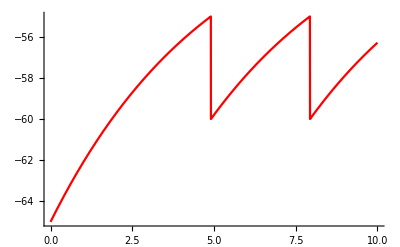

```mathematica
Plot[usol[t],{t,0,10},PlotRange->All,PlotStyle->{Red}]
```